## Rob’s analysis

```mathematica
σx=3*10^(-3)*mhe/ℏ;
σy=12*10^(-3)*mhe/ℏ;
σz=8.5*10^(-3)*mhe/ℏ;
```

```mathematica
Clear["Global`*"]
ℏ=1.054*10^(-34);
mhe=6.64331*10^(-27);
kL=4.10165*10^6;
```

```mathematica
λ[k_,σ_]:=k/(2*σ);
α[σ_,k_]:=(Exp[-2*λ[k,σ]^2]-1+Sqrt[2*Pi]*λ[k,σ]*Erf[Sqrt[2]*λ[k,σ]]);
A[σ_,k_,Δt_,tc_]:=(kL*σ*ℏ/mhe)*(Δt-tc);
β[σ_,k_,Δt_,tc_]:=Exp[-2*λ[k,σ]^2]*Cos[4*A[σ,k,Δt,tc]*λ[k,σ]]-1+2*Sqrt[2]*A[σ,k,Δt,tc]*DawsonF[Sqrt[2]*A[σ,k,Δt,tc]]+Sqrt[Pi/2]*Exp[-2*A[σ,k,Δt,tc]^2]*((λ[k,σ]-I*A[σ,k,Δt,tc])*Erf[Sqrt[2]*λ[k,σ]-Sqrt[2]*I*A[σ,k,Δt,tc]]+(λ[k,σ]+I*A[σ,k,Δt,tc])*Erf[Sqrt[2]*λ[k,σ]+Sqrt[2]*I*A[σ,k,Δt,tc]]);
g12[k_,σ_,h_,ϕ_]:=Product[i^2,{i,k}]+h/2*Product[i,{i,α[σ,k]*4*σ^2}]-h/2*Product[i,{i,α[σ,k]*4*σ^2}]*Cos[ϕ];
Ev[k_,σ_,h_,Δt_,tc_]:=h*Product[i,{i,α[σ[[1;;2]],k[[1;;2]]]}]*β[σ[[3]],k[[3]],Δt,tc]/(h*Product[i,{i,α[σ[[1;;2]],k[[1;;2]]]}]*β[σ[[3]],k[[3]],Δt,tc]+16*Product[i,{i,λ[k,σ]^2}]);
r[k_,σ_,h_,ϕ_]:=h/2*Product[i,{i,α[σ,k]}]/Product[i^2,{i,λ[k,σ]}];
```

```mathematica
g12[{0.052,0.53,0.47}*10^6,{0.034,0.3,0.3}*10^6,27,Pi/2]/Product[i^2,{i,{0.052,0.53,0.47}*10^6}]
Ev[{0.63,0.63,0.63}*10^6,{0.378,5.04,5.04}*10^6,2]
r[{0.052,0.53,0.47}*10^6,{0.034,0.3,0.3}*10^6*6,3,Pi/2]
α[{0.378,5.04,5.04}*10^6,{0.63,0.63,0.63}*10^6]
λ[{0.63,0.63,0.63}*10^6,{0.378,5.04,5.04}*10^6]
Product[i^2,{i,λ[{0.052,0.53,0.47}*10^6,{0.034,0.3,0.3}*10^6]}]
```

8.64049

0.449833

1.47289

{0.569277,0.00390117,0.00390117}

{0.833333,0.0625,0.0625}

0.279983

```mathematica
(4.352847843498329-1)/(4.352847843498329+1)
```

0.626367

```mathematica
+1)
```

{124.331,124.331,124.331}

0.279983

```mathematica
temp[[1;;2]]
```

{2,2}

```mathematica
temp={2,2,2};
```

```mathematica
Product[i^2,{i,{0.052,0.53,0.47}*10^6}]
3/2*Product[i,{i,α[{0.063,0.063,0.063}*10^1*4,{0.0063,0.0063,0.0063}*10^6]*{0.063,0.063,0.063}*10^1*4}]
```

1.67785×10^32

7.37695×10^11

```mathematica
62.12389111404524/28
```

2.21871

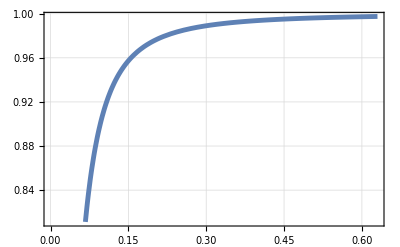

```mathematica
Plot[Product[i,{i,λ[{0.063,0.063,0.063}*10^6,{σ,σ,σ}*10^6]^(-2)*α[{σ,σ,σ}*10^6,{0.063,0.063,0.063}*10^6]}],{σ,0,0.063*10}]
```

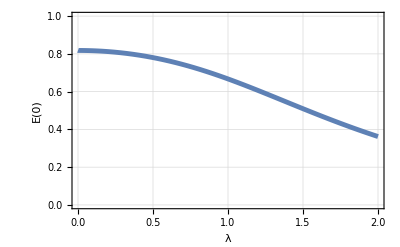

```mathematica
Plot[Ev[{σx,σy,σz}*2*x,{σx,σy,σz},9,1,1],{x,0.0,2},FrameLabel -> {"λ", "E(0)"},PlotRange->{{0,2},{0,1}}]
```

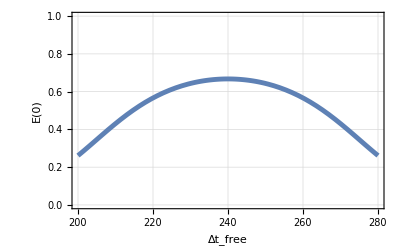

```mathematica
Plot[Ev[{σx,σy,σz}*2,{σx,σy,σz},9,x*10^(-6),240*10^(-6)],{x,200,280},FrameLabel -> {"Δt_free", "E(0)"},PlotRange->{{200,280},{0.0,1}}]
```

```mathematica
GravCoeff[g_,k0_,tc_,tsep_]:=Exp[-2*g^2*k0^2*tc^2*tsep^2-4*I*g*k0*tc^2]*(1+Erf[I*g*k0*tc*tsep])^2
```

```mathematica
Abs[GravCoeff[9.81,kL,240*10^(-6),63*10^(-6)]]
```

0.768291

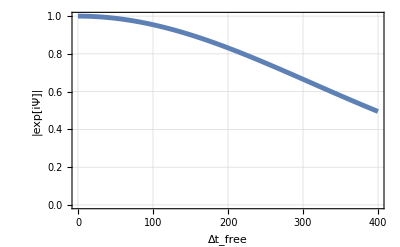

```mathematica
Plot[Abs[GravCoeff[9.81,kL,x*10^(-6),63*10^(-6)]],{x,0,400},FrameLabel -> {"Δt_free", "|exp[iΨ]|"},PlotRange->{{0,400},{0.0,1}}]
```

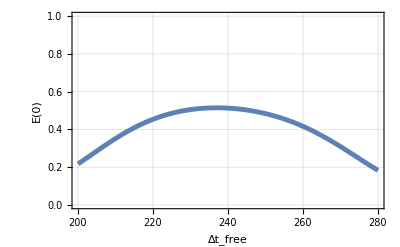

```mathematica
Plot[Ev[{σx,σy,σz}*2,{σx,σy,σz},9,x*10^(-6),240*10^(-6)]*Abs[GravCoeff[9.81,kL,x*10^(-6),63*10^(-6)]],{x,200,280},FrameLabel -> {"Δt_free", "E(0)"},PlotRange->{{200,280},{0.0,1}}]
```

```mathematica
FullSimplify[(2*Sqrt[x*(1+x)*y*(1+y)])/(3*x^2+3*y^2+x+y)/.{y->yi-x}]
```

(2 √(x (1+x) (-x+yi) (1-x+yi)))/(6 x^2+yi-6 x yi+3 yi^2)

```mathematica
Expand[x (1+x) (-x+yi) (1-x+yi)]
```

-x^2+x^4+x yi-x^2 yi-2 x^3 yi+x yi^2+x^2 yi^2

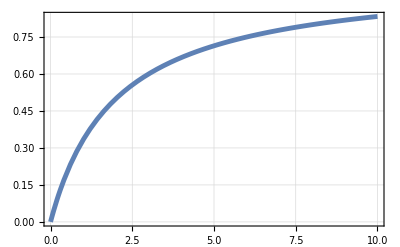

1.

```mathematica
Plot[h/(2+h),{h,0,10}]
```